```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
plotsDir= "../../plots/plots-105";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../runs/Trials/N9K9/81027575.dat"];
```

$Aborted

```mathematica
changeNK[9, 9];
```

```mathematica
matdata = cMat[data];
```

```mathematica
eig = Flatten@(Eigenvalues/@matdata[[All, 2]]);
```

```mathematica
tr = Tr[#.#]&/@matdata[[All, 2]]//Chop;
```

```mathematica
higher = Tr[MatrixPower[#, 10]]&/@matdata[[All, 2]]//Chop;
```

```mathematica
plts = Monitor[Table[Module[{}, (
obsSim[n] = Tr[MatrixPower[#, n]]&/@matdata[[All, 2]]//Chop//Re;
obsUnitary[n] = Tr[MatrixPower[#, n]]&/@unitMats//Chop//Re;

Histogram[{Standardize[obsSim[n]], Standardize[obsUnitary[n]]}, 3000, PDF, ImageSize->500]
)], {n, 2, 13}], ProgressIndicator[(n-2)/(13-2)]];
```

$Aborted

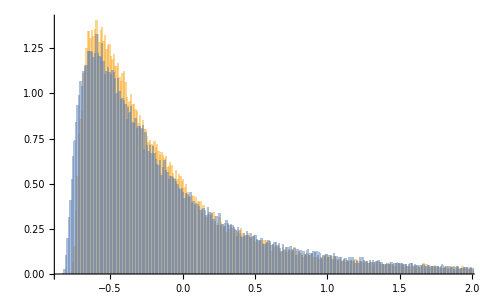

```mathematica
Histogram[{Standardize[higher//Re], Standardize[unitHigher//Re]}, 3000, PDF]
```

```mathematica
Standardize[higher][[1]]
```

12.0723

```mathematica
unitHigher//Re
```

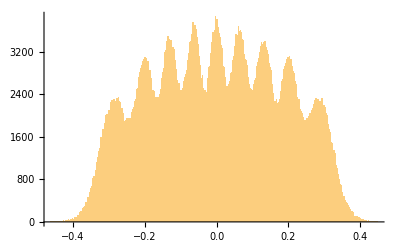

```mathematica
Histogram[eig, 300]
```

```mathematica
symMats = RandomVariate[GaussianSymplecticMatrixDistribution[1, 9], 100000];
```

```mathematica
symEigs = Flatten[Eigenvalues/@symMats];
```

```mathematica
symHigher = Tr[MatrixPower[#, 6]]&/@symMats//Chop;
```

```mathematica
plt = Histogram[{(eig-μp)/σp,(symEigs-μ)/σ}, 300, PDF,
ChartLegends->{"Simulation", "Random Symplectic"},
AxesLabel->{"eigenvalue", "PDF"},
PlotLabel->"Distribution of Eigenvalues of X1 across time",
ImageSize->600
];
```

```mathematica
Export[plotsDir<>"/eigDist-Symplectic.pdf", Rasterize[plt, ImageResolution->300, ImageSize->500]]
```

../../plots/plots-104/eigDist-Symplectic.pdf

```mathematica
unitMats = RandomVariate[GaussianUnitaryMatrixDistribution[1, 9], 100000];
```

```mathematica
unitHigher = Tr[MatrixPower[#, 10]]&/@unitMats//Chop;
```

```mathematica
unitEigs = Flatten[Eigenvalues/@unitMats];
μ3 = Mean[unitEigs];
σ3 = StandardDeviation[unitEigs];
```

```mathematica
unitTrs = Tr[#.#]&/@unitMats//Chop;
```

```mathematica
plt2 = Histogram[{(eig-μp)/σp,(unitEigs-μ3)/σ3}, 300, PDF,
ChartLegends->{"Simulation", "Random Unitary"},
AxesLabel->{"eigenvalue", "PDF"},
PlotLabel->"Distribution of Eigenvalues of X1 across time",
ImageSize->600
];
```

```mathematica
Export[plotsDir<>"/eigDist-Unitary.pdf", Rasterize[plt2, ImageResolution->300, ImageSize->500]]
```

../../plots/plots-104/eigDist-Unitary.pdf

```mathematica
symTrs = Tr[#.#]&/@symMats//Chop;
```

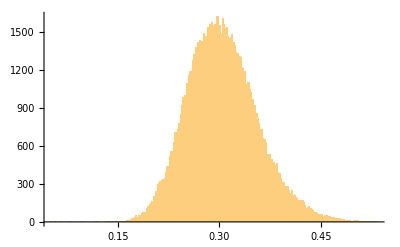

```mathematica
Histogram[tr, 300]
```

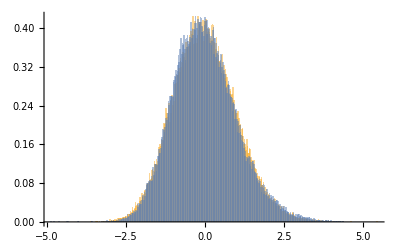

```mathematica
Histogram[{Standardize[symTrs], Standardize[tr]}, 300, PDF]
```

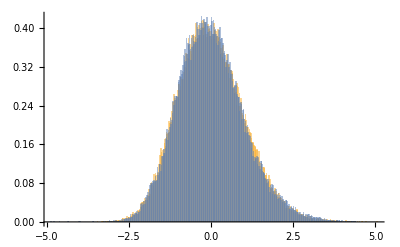

```mathematica
Histogram[{Standardize[unitTrs], Standardize[tr]}, 300, PDF]
```

```mathematica
orthoMats = RandomVariate[GaussianOrthogonalMatrixDistribution[1, $N], 100000];
orthoEigs = Flatten[Eigenvalues/@orthoMats];
orthoTrs = Tr[#.#]&/@orthoMats//Chop;
```

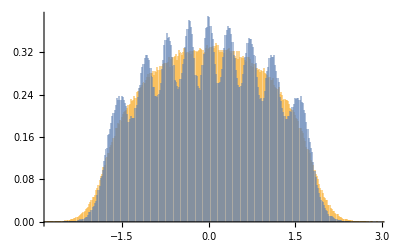

```mathematica
Histogram[{Standardize[orthoEigs], Standardize[eig]}, 300, PDF]
```

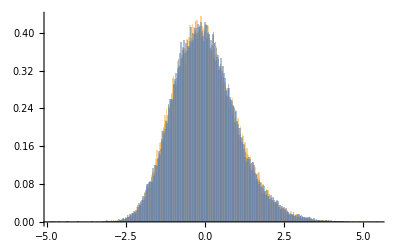

```mathematica
Histogram[{Standardize[orthoTrs], Standardize[tr]}, 300, PDF]
```

```mathematica
σ = Sqrt[Mean@(tr/symTrs)];
```

```mathematica
σ
```

0.0317551

```mathematica
Min[eig]
```

-0.460517

```mathematica
Max[eig]
```

0.446189

```mathematica
Min[symEigs]
```

-9.47481

```mathematica
Max[symEigs]
```

9.60757

```mathematica
μ = Mean[symEigs]
```

-0.000872824

```mathematica
σ = StandardDeviation[symEigs]
```

4.12407

```mathematica
μp = Mean[eig];
σp = StandardDeviation[eig];
```